### Константы

```mathematica
If[True,
A            =- 0.024 ;
B            = 1.69 ;
CC          = 0.5 ;
α            = 10^-5                 (* K^-1 *);
Subscript[T, 0]          = 300                  (* K *);
Subscript[T, avg]       = 300                  (* K *);
Young   = 1.75 * 10^11  (* Па *);
σf          = 1.1 * 10^8      (* Па *);
ϵf          = 0.000628571 ;
l            = 10                     (* Длина стержня *);
Subscript[T, f]          =1                      (* Конечный момент времени *); 
Subscript[h, t]            = 0.05              (* Шаг времени *);
a            = 50                     (* Просто константа *);
n            =  10                      (* Число узлов сетки *);
Subscript[h, x]          = l/(n-1)                   (* Шаг сетки *);
];
```

### Определение функций распределения температуры в пространстве и времени

```mathematica
F[x_] := a Sin[(π x)/l];
Subscript[T, 1][x_, t_] := Subscript[T, avg] + F[x]t Sin[t];
Subscript[T, 2][ x_, t_ ] := Subscript[T, avg] + F[x] Cos[π t^2](t+1);
TT = Subscript[T, 1];
```

Тепловые деформации

```mathematica
Subscript[ϵ, t] [x_,tt_] := α(TT[x, tt] - Subscript[T, 0]);
```

```mathematica
Subscript[u, analytical] = First[Flatten[
DSolve[{D[D[u[x,t], x]-Subscript[ϵ, t][x, t], x]== 0,
u[0, t] == 0, 
u[l, t] == 0},
u[x,t],{x, t}]]]⟦2⟧  // FullSimplify
```

-(t (-5+x+5 Cos[(π x)/10]) Sin[t])/(1000 π)

### Численное решение (метод конечных разностей)

```mathematica
points = Table[i*Subscript[h, x], {i, 0, n-1}]
στ = Table[0,{i, 1, n}];                                     (* значения напряжений во временном слое τ *)
σfv = Table[σf,{i, 1, n}];                                (* значения переменных пределов прочности *)
ϵτ = Table[0,{i, 1, n}];                                            (* значения полных деформаций во временном слое τ *)
ϵe = Table[0,{i, 1, n}];                                     (* значения упругих деформаций во временном слое τ *)
ϵT = Table[0,{i, 1, n}];                                            (* значения температурных деформаций во временном слое τ *) 
ϵcrk = Table[0,{i, 1, n}];                                        (* значения деформаций за счет трещин *) 
Tτ = Table[0,{i, 1, n}];                                            (* значения температуры во временном слое τ *) 
Subscript[balance, normal] [x_,k_]:= Young x;                             (* функция, подставляемая в условие равновесия при напряжениях, меньших предельных *) 
Subscript[dbalance, normal][xx_, k_] := D[Subscript[balance, normal][x, k], x] /. x-> xx;
Subscript[balance, crack][x_,k_]:=  σfv⟦k⟧(A + B ⅇ^(-CC x/ϵf));   (* функция, подставляемая в условие равновесия при напряжениях, больших предельных *) 
Subscript[dbalance, crack][xx_,k_] := D[Subscript[balance, crack][x, k], x] /. x-> xx;
balances =  Table[0,{i, 1, n}];                              (* функции равновесий на временном слое τ *) 
left = Table[0,{i, 1, n}];                           (* линеаризованные уравнения, решениями которых являются перемещения на временном слое τ *) 
right = Table[0,{i, 1, n}];                           (* линеаризованные уравнения, решениями которых являются перемещения на временном слое τ *) 
shifts = Table[0,{i, 1, n}];                                 (* сами перемещения *) 
cracking = Table[False,{i, 1, n}] ;                 (* нужно ли менять предел прочности*)
data = {};
debug = True;
```

{0,10/9,20/9,10/3,40/9,50/9,20/3,70/9,80/9,10}

Подготавливаем левую часть линеаризованной системы. При решении СЛАУ она будет оставаться постоянной, меняется только правая часть на каждой итерации метода Ньютона

```mathematica
left ={{1}~Join~ConstantArray[0, n-1]}~Join~Table[
Table[If[
Between[j, {i-1, i+1}], 
If[j == i, -2, 1],0], 
{j, 1, n}],
{i, 2, n-1}]~Join~{ConstantArray[0, n-1]~Join~{1}};
For[τ = 0,τ≤Subscript[T, f],τ=τ+Subscript[h, t], (*каждый временной слой*)
If[False, Break[]];
temp = {};
For [i = 1, i≤ n, ++i,
Tτ⟦i⟧= TT[points⟦i⟧, τ];
ϵT⟦i⟧ = Subscript[ϵ, t][points⟦i⟧, τ];
memory =Young*( ϵτ⟦i⟧ - ϵT⟦i⟧ - ϵcrk⟦i⟧); 
balances⟦i⟧ = If[memory < σfv⟦i⟧, 
cracking⟦i⟧ = False;Subscript[balance, normal],
cracking⟦i⟧ = True; Subscript[balance, crack]];];
iterations = 0;
Print[Style[τ,Red,30] ];(*временной слой*)
While[(Norm[(shifts - previous)/(Norm@previous + 10^-20)] ≥ 10^-5  && iterations < 30)|| iterations == 0,
++iterations; 
For[i = 2, i < n, ++i,
Subscript[nonElastic, i] = If[cracking⟦i⟧, ϵT⟦i⟧, ϵT⟦i⟧ + ϵcrk⟦i⟧]; Subscript[nonElastic, i-1] = If[cracking⟦i⟧, ϵT⟦i-1⟧, ϵT⟦i-1⟧ + ϵcrk⟦i-1⟧];
Subscript[v, i]= (shifts⟦i+1⟧ - shifts⟦i⟧)/Subscript[h, x] - Subscript[nonElastic, i]*If[debug, 1, 0]; Subscript[v, i-1]=(shifts⟦i⟧ - shifts⟦i-1⟧)/Subscript[h, x] - Subscript[nonElastic, i-1]*If[debug, 1, 0];
If[cracking⟦i⟧,
Subscript[dσ, i] = Subscript[dbalance, crack][Subscript[v, i], i]; Subscript[dσ, i-1] = Subscript[dbalance, crack][Subscript[v, i-1], i], 
Subscript[dσ, i] = Subscript[dbalance, normal][Subscript[v, i], i]; Subscript[dσ, i-1] = Subscript[dbalance, normal][Subscript[v, i-1], i];
];
right⟦i⟧ = Subscript[h, x](Subscript[v, i] +  Subscript[nonElastic, i]*If[debug, 1, 0]) - Subscript[h, x]( Subscript[v, i-1] +  Subscript[nonElastic, i-1]*If[debug, 1, 0]) - (Subscript[h, x] balances⟦i⟧[Subscript[v, i], i])/Subscript[dσ, i]+ (Subscript[h, x] balances⟦i⟧[Subscript[v, i-1], i])/Subscript[dσ, i-1];
];
previous = shifts;
shifts = Flatten@LinearSolve[left, right];
Print@{MatrixForm@right, shifts};
];
For [i=1, i< n, ++i,
ϵτ⟦i⟧ = (shifts⟦i+1⟧ - shifts⟦i⟧)/Subscript[h, x];
If[cracking⟦i⟧,
σfv⟦i⟧=balances⟦i⟧[ϵτ⟦i⟧ - ϵT⟦i⟧, i]; στ⟦i⟧ = σfv⟦i⟧; ϵe⟦i⟧ = στ⟦i⟧/Young; ϵcrk⟦i⟧ = ϵτ⟦i⟧ - ϵT⟦i⟧ - ϵe⟦i⟧ ,
ϵe⟦i⟧ = ϵτ⟦i⟧ -ϵT⟦i⟧-ϵcrk⟦i⟧; στ⟦i⟧ = balances⟦i⟧[ϵe⟦i⟧, i]; ];
AppendTo[temp, {τ, Tτ⟦i⟧, στ⟦i⟧, ϵτ⟦i⟧, ϵτ⟦i⟧-ϵT⟦i⟧, ϵcrk⟦i⟧, ϵe⟦i⟧}]];
AppendTo[data, temp];];
```

0

{(0
0.
0.
0.
0.
0.
0.
0.
0.
0),{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

0.05

{(0
4.7483×10^-7
4.17559×10^-7
3.09923×10^-7
1.64907×10^-7
0.
-1.64907×10^-7
-3.09923×10^-7
-4.17559×10^-7
0),{0.,-8.74833×10^-7,-1.27484×10^-6,-1.25728×10^-6,-9.29802×10^-7,-4.37417×10^-7,5.49689×10^-8,3.82448×10^-7,4.00003×10^-7,0.}}

{(0
4.7483×10^-7
4.17559×10^-7
3.09923×10^-7
1.64907×10^-7
-1.05879×10^-22
-1.64907×10^-7
-3.09923×10^-7
-4.17559×10^-7
0),{0.,-8.74833×10^-7,-1.27484×10^-6,-1.25728×10^-6,-9.29802×10^-7,-4.37417×10^-7,5.49689×10^-8,3.82448×10^-7,4.00003×10^-7,0.}}

0.1

{(0
1.89695×10^-6
1.66815×10^-6
1.23814×10^-6
6.58803×10^-7
0.
-6.58803×10^-7
-1.23814×10^-6
-1.66815×10^-6
0),{0.,-3.49496×10^-6,-5.09297×10^-6,-5.02284×10^-6,-3.71456×10^-6,-1.74748×10^-6,2.19601×10^-7,1.52788×10^-6,1.59801×10^-6,0.}}

{(0
1.89695×10^-6
1.66815×10^-6
1.23814×10^-6
6.58803×10^-7
-8.47033×10^-22
-6.58803×10^-7
-1.23814×10^-6
-1.66815×10^-6
0),{0.,-3.49496×10^-6,-5.09297×10^-6,-5.02284×10^-6,-3.71456×10^-6,-1.74748×10^-6,2.19601×10^-7,1.52788×10^-6,1.59801×10^-6,0.}}

0.15

{(0
4.25924×10^-6
3.74551×10^-6
2.78002×10^-6
1.47922×10^-6
0.
-1.47922×10^-6
-2.78002×10^-6
-3.74551×10^-6
0),{0.,-7.84728×10^-6,-0.0000114353,-0.0000112778,-8.34035×10^-6,-3.92364×10^-6,4.93073×10^-7,3.43057×10^-6,3.58804×10^-6,0.}}

{(0
4.25924×10^-6
3.74551×10^-6
2.78002×10^-6
1.47922×10^-6
0.
-1.47922×10^-6
-2.78002×10^-6
-3.74551×10^-6
0),{0.,-7.84728×10^-6,-0.0000114353,-0.0000112778,-8.34035×10^-6,-3.92364×10^-6,4.93073×10^-7,3.43057×10^-6,3.58804×10^-6,0.}}

0.2

{(0
7.54988×10^-6
6.63925×10^-6
4.92783×10^-6
2.62205×10^-6
0.
-2.62205×10^-6
-4.92783×10^-6
-6.63925×10^-6
0),{0.,-0.00001391,-0.0000202701,-0.000019991,-0.000014784,-6.955×10^-6,8.74015×10^-7,6.08098×10^-6,6.36012×10^-6,0.}}

{(0
7.54988×10^-6
6.63925×10^-6
4.92783×10^-6
2.62205×10^-6
0.
-2.62205×10^-6
-4.92783×10^-6
-6.63925×10^-6
0),{0.,-0.00001391,-0.0000202701,-0.000019991,-0.000014784,-6.955×10^-6,8.74015×10^-7,6.08098×10^-6,6.36012×10^-6,0.}}

0.25

{(0
0.0000117524
0.0000103349
7.67082×10^-6
4.08156×10^-6
0.
-4.08156×10^-6
-7.67082×10^-6
-0.0000103349
0),{0.,-0.0000216527,-0.0000315531,-0.0000311186,-0.0000230133,-0.0000108264,1.36052×10^-6,9.46585×10^-6,9.90036×10^-6,0.}}

{(0
0.0000117524
0.0000103349
7.67082×10^-6
4.08156×10^-6
-3.38813×10^-21
-4.08156×10^-6
-7.67082×10^-6
-0.0000103349
0),{0.,-0.0000216527,-0.0000315531,-0.0000311186,-0.0000230133,-0.0000108264,1.36052×10^-6,9.46585×10^-6,9.90036×10^-6,0.}}

0.3

{(0
0.0000168456
0.0000148138
0.0000109952
5.85043×10^-6
5.0822×10^-21
-5.85043×10^-6
-0.0000109952
-0.0000148138
0),{0.,-0.0000310366,-0.0000452276,-0.0000446048,-0.0000329868,-0.0000155183,1.95014×10^-6,0.0000135682,0.000014191,0.}}

{(0
0.0000168456
0.0000148138
0.0000109952
5.85043×10^-6
6.77626×10^-21
-5.85043×10^-6
-0.0000109952
-0.0000148138
0),{0.,-0.0000310366,-0.0000452276,-0.0000446048,-0.0000329868,-0.0000155183,1.95014×10^-6,0.0000135682,0.000014191,0.}}

0.35

{(0
0.000022804
0.0000200535
0.0000148843
7.91976×10^-6
3.38813×10^-21
-7.91976×10^-6
-0.0000148843
-0.0000200535
0),{0.,-0.0000420145,-0.0000612249,-0.0000603818,-0.0000446544,-0.0000210072,2.63992×10^-6,0.0000183673,0.0000192104,0.}}

{(0
0.000022804
0.0000200535
0.0000148843
7.91976×10^-6
0.
-7.91976×10^-6
-0.0000148843
-0.0000200535
0),{0.,-0.0000420145,-0.0000612249,-0.0000603818,-0.0000446544,-0.0000210072,2.63992×10^-6,0.0000183673,0.0000192104,0.}}

0.4

{(0
0.0000295975
0.0000260276
0.0000193184
0.0000102791
0.
-0.0000102791
-0.0000193184
-0.0000260276
0),{0.,-0.0000545309,-0.0000794642,-0.00007837,-0.0000579573,-0.0000272654,3.42637×10^-6,0.0000238391,0.0000249334,0.}}

{(0
0.0000295975
0.0000260276
0.0000193184
0.0000102791
0.
-0.0000102791
-0.0000193184
-0.0000260276
0),{0.,-0.0000545309,-0.0000794642,-0.00007837,-0.0000579573,-0.0000272654,3.42637×10^-6,0.0000238391,0.0000249334,0.}}

0.45

{(0
0.0000371917
0.0000327059
0.0000242752
0.0000129166
0.
-0.0000129166
-0.0000242752
-0.0000327059
0),{0.,-0.0000685226,-0.0000998534,-0.0000984783,-0.0000728281,-0.0000342613,4.30552×10^-6,0.0000299558,0.0000313308,0.}}

{(0
0.0000371917
0.0000327059
0.0000242752
0.0000129166
0.
-0.0000129166
-0.0000242752
-0.0000327059
0),{0.,-0.0000685226,-0.0000998534,-0.0000984783,-0.0000728281,-0.0000342613,4.30552×10^-6,0.0000299558,0.0000313308,0.}}

0.5

{(0
0.0000455481
0.0000400543
0.0000297294
0.0000158187
0.
-0.0000158187
-0.0000297294
-0.0000400543
0),{0.,-0.0000839184,-0.000122289,-0.000120605,-0.0000891913,-0.0000419592,5.2729×10^-6,0.0000366863,0.0000383703,0.}}

{(0
0.0000455481
0.0000400543
0.0000297294
0.0000158187
0.
-0.0000158187
-0.0000297294
-0.0000400543
0),{0.,-0.0000839184,-0.000122289,-0.000120605,-0.0000891913,-0.0000419592,5.2729×10^-6,0.0000366863,0.0000383703,0.}}

0.55

{(0
0.000054624
0.0000480356
0.0000356533
0.0000189707
0.
-0.0000189707
-0.0000356533
-0.0000480356
0),{0.,-0.00010064,-0.000146656,-0.000144636,-0.000106964,-0.00005032,6.32358×10^-6,0.0000439964,0.000046016,0.}}

{(0
0.000054624
0.0000480356
0.0000356533
0.0000189707
0.
-0.0000189707
-0.0000356533
-0.0000480356
0),{0.,-0.00010064,-0.000146656,-0.000144636,-0.000106964,-0.00005032,6.32358×10^-6,0.0000439964,0.000046016,0.}}

0.6

{(0
0.000064373
0.0000566087
0.0000420165
0.0000223565
0.
-0.0000223565
-0.0000420165
-0.0000566087
0),{0.,-0.000118602,-0.00017283,-0.00017045,-0.000126054,-0.0000593009,7.45217×10^-6,0.0000518487,0.0000542287,0.}}

{(0
0.000064373
0.0000566087
0.0000420165
0.0000223565
0.
-0.0000223565
-0.0000420165
-0.0000566087
0),{0.,-0.000118602,-0.00017283,-0.00017045,-0.000126054,-0.0000593009,7.45217×10^-6,0.0000518487,0.0000542287,0.}}

0.65

{(0
0.0000747449
0.0000657296
0.0000487863
0.0000259586
0.
-0.0000259586
-0.0000487863
-0.0000657296
0),{0.,-0.000137711,-0.000200677,-0.000197914,-0.000146364,-0.0000688555,8.65288×10^-6,0.0000602026,0.0000629661,0.}}

{(0
0.0000747449
0.0000657296
0.0000487863
0.0000259586
0.
-0.0000259586
-0.0000487863
-0.0000657296
0),{0.,-0.000137711,-0.000200677,-0.000197914,-0.000146364,-0.0000688555,8.65288×10^-6,0.0000602026,0.0000629661,0.}}

0.7

{(0
0.000085686
0.000075351
0.0000559276
0.0000297584
0.
-0.0000297584
-0.0000559276
-0.000075351
0),{0.,-0.000157869,-0.000230052,-0.000226884,-0.000167788,-0.0000789345,9.91948×10^-6,0.000069015,0.000072183,0.}}

{(0
0.000085686
0.000075351
0.0000559276
0.0000297584
0.
-0.0000297584
-0.0000559276
-0.000075351
0),{0.,-0.000157869,-0.000230052,-0.000226884,-0.000167788,-0.0000789345,9.91948×10^-6,0.000069015,0.000072183,0.}}

0.75

{(0
0.0000971392
0.0000854228
0.0000634031
0.0000337361
0.
-0.0000337361
-0.0000634031
-0.0000854228
0),{0.,-0.000178971,-0.000260802,-0.000257211,-0.000190216,-0.0000894853,0.0000112454,0.0000782399,0.0000818314,0.}}

{(0
0.0000971392
0.0000854228
0.0000634031
0.0000337361
0.
-0.0000337361
-0.0000634031
-0.0000854228
0),{0.,-0.000178971,-0.000260802,-0.000257211,-0.000190216,-0.0000894853,0.0000112454,0.0000782399,0.0000818314,0.}}

0.8

{(0
0.000109045
0.0000958922
0.0000711738
0.0000378708
0.
-0.0000378708
-0.0000711738
-0.0000958922
0),{0.,-0.000200905,-0.000292766,-0.000288734,-0.000213529,-0.000100453,0.0000126236,0.000087829,0.0000918606,0.}}

{(0
0.000109045
0.0000958922
0.0000711738
0.0000378708
0.
-0.0000378708
-0.0000711738
-0.0000958922
0),{0.,-0.000200905,-0.000292766,-0.000288734,-0.000213529,-0.000100453,0.0000126236,0.000087829,0.0000918606,0.}}

0.85

{(0
0.000121339
0.000106704
0.0000791984
0.0000421406
2.71051×10^-20
-0.0000421406
-0.0000791984
-0.000106704
0),{0.,-0.000223556,-0.000325774,-0.000321288,-0.000237603,-0.000111778,0.0000140469,0.0000977314,0.000102218,0.}}

{(0
0.000121339
0.000106704
0.0000791984
0.0000421406
2.71051×10^-20
-0.0000421406
-0.0000791984
-0.000106704
0),{0.,-0.000223556,-0.000325774,-0.000321288,-0.000237603,-0.000111778,0.0000140469,0.0000977314,0.000102218,0.}}

0.9

{(0
0.000133957
0.0001178
0.0000874341
0.0000465227
0.
-0.0000465227
-0.0000874341
-0.0001178
0),{0.,-0.000246804,-0.000359651,-0.000354698,-0.000262311,-0.000123402,0.0000155076,0.000107894,0.000112847,0.}}

{(0
0.000133957
0.0001178
0.0000874341
0.0000465227
0.
-0.0000465227
-0.0000874341
-0.0001178
0),{0.,-0.000246804,-0.000359651,-0.000354698,-0.000262311,-0.000123402,0.0000155076,0.000107894,0.000112847,0.}}

0.95

{(0
0.00014683
0.00012912
0.0000958366
0.0000509936
0.
-0.0000509936
-0.0000958366
-0.00012912
0),{0.,-0.000270522,-0.000394213,-0.000388785,-0.00028752,-0.000135261,0.0000169979,0.000118263,0.000123692,0.}}

{(0
0.00014683
0.00012912
0.0000958366
0.0000509936
0.
-0.0000509936
-0.0000958366
-0.00012912
0),{0.,-0.000270522,-0.000394213,-0.000388785,-0.00028752,-0.000135261,0.0000169979,0.000118263,0.000123692,0.}}

1.

{(0
0.000159889
0.000140604
0.00010436
0.0000555288
0.
-0.0000555288
-0.00010436
-0.000140604
0),{0.,-0.000294581,-0.000429274,-0.000423363,-0.000313091,-0.000147291,0.0000185096,0.000128781,0.000134693,0.}}

{(0
0.000159889
0.000140604
0.00010436
0.0000555288
0.
-0.0000555288
-0.00010436
-0.000140604
0),{0.,-0.000294581,-0.000429274,-0.000423363,-0.000313091,-0.000147291,0.0000185096,0.000128781,0.000134693,0.}}

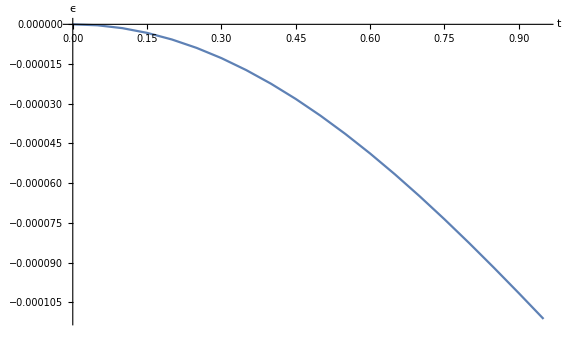

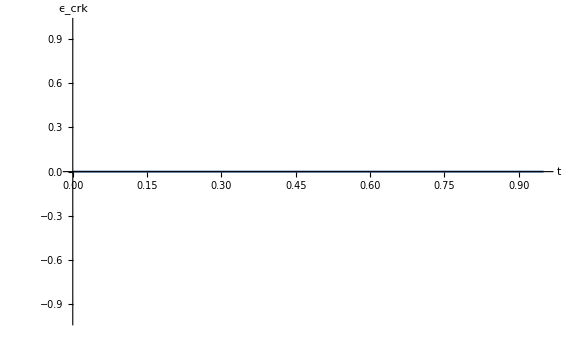

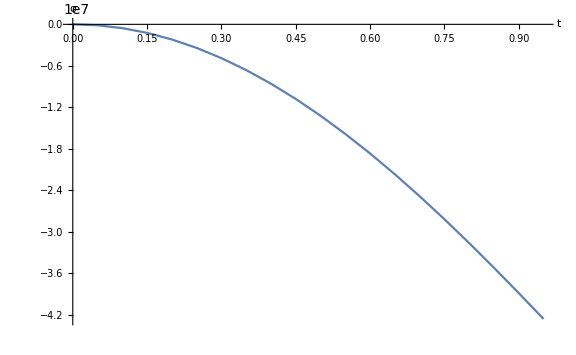

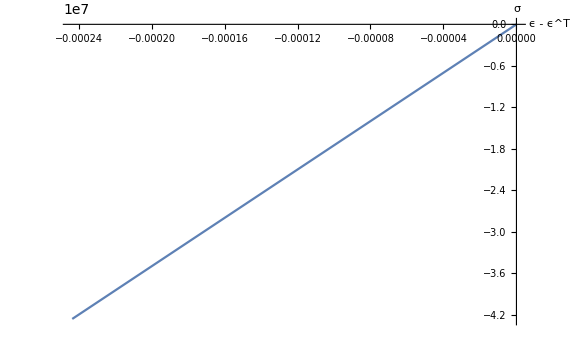

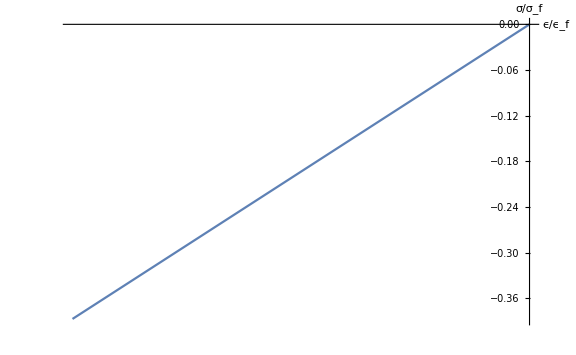

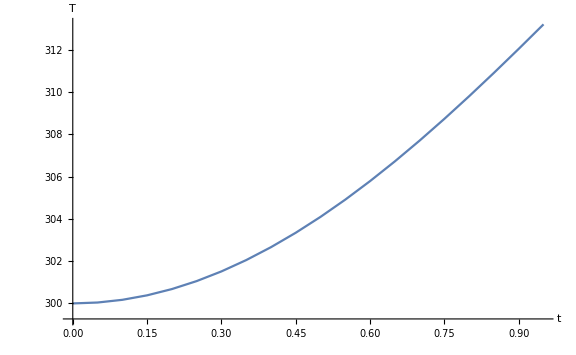

```mathematica
node = 2; 
tϵ = ListPlot[Table[{data⟦τ, node, 1⟧, data⟦τ, node, 4⟧}, {τ, 1,IntegerPart@ (Subscript[T, f]/Subscript[h, t])}], Joined->True,ImageSize->Large, AxesLabel->{"t", "ϵ"},AxesStyle->Black]
tϵcrk = ListPlot[Table[{data⟦τ, node, 1⟧, data⟦τ, node, 6⟧}, {τ, 1,IntegerPart@ (Subscript[T, f]/Subscript[h, t])}], Joined->True,ImageSize->Large,  AxesLabel->{"t", "ϵ_crk"},AxesStyle->Black]
tσ = ListPlot[Table[{data⟦τ, node, 1⟧, data⟦τ, node, 3⟧}, {τ, 1,IntegerPart@ (Subscript[T, f]/Subscript[h, t])}], Joined->True,ImageSize->Large,  AxesLabel->{"t", "σ"},AxesStyle->Black]
dϵσ = ListPlot[Table[{data⟦τ, node, 5⟧, data⟦τ, node, 3⟧}, {τ, 1,IntegerPart@ (Subscript[T, f]/Subscript[h, t])}], Joined->True, ImageSize->Large,AxesLabel->{"ϵ - ϵ^T", "σ"},AxesStyle->Black]
normdϵσ = ListPlot[Table[{data⟦τ, node, 4⟧/ϵf, data⟦τ, node, 3⟧/σf}, {τ, 1,IntegerPart@ (Subscript[T, f]/Subscript[h, t])}], Joined->True,ImageSize->Large, Ticks->{Table[i,{i,1,10}], Automatic},AxesLabel->{"ϵ/ϵ_f", "σ/σ_f"},AxesStyle->Black]
tT = ListPlot[Table[{data⟦τ, node, 1⟧, data⟦τ, node, 2⟧}, {τ, 1,IntegerPart@ (Subscript[T, f]/Subscript[h, t])}], Joined->True, ImageSize->Large,AxesLabel->{"t", "T"},AxesStyle->Black ]
```

### Сохраняем графики

```mathematica
If[False, 
SetDirectory[NotebookDirectory[]];
options =StringJoin[ToString@TT~StringJoin~"/", StringJoin["h_", ToString[h] ~StringJoin~"_"], StringJoin["tau_", ToString[τ]]];
With[
{directory=FileNameJoin[{ParentDirectory@NotebookDirectory[], StringJoin["LaTeX/pic/",options ]}]},
Switch[FileType[directory],
None,CreateDirectory[directory],
Directory, Print["Overriding files in directory: "~StringJoin~directory]
];
Export[FileNameJoin[{directory, "epsilon(t).pdf"}], tϵ];
Export[FileNameJoin[{directory, "epsilon_crk(t).pdf"}], tϵcrk];
Export[FileNameJoin[{directory, "sigma(t).pdf"}], tσ];
Export[FileNameJoin[{directory, "sigma(epsilon).pdf"}], dϵσ];
Export[FileNameJoin[{directory, "norm_sigma(epsilon).pdf"}], normdϵσ];
Export[FileNameJoin[{directory, "T(t).pdf"}], tT];
]
];
```

```mathematica
left//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
D[ϵT[T1[x,t]],{x,1}]
```

{0,0,0,0,0,0,0,0,0,0}[T1[x,t]]+{0.,0.0001439,0.000270444,0.000364368,0.000414344,0.000414344,0.000364368,0.000270444,0.0001439,0.}'[T1[x,t]] T1^(1,0)[x,t]